# Numeric Integration Test

## Numeric Integration Rule One Dimensional

```mathematica
i = 2;
p = 6;
```

```mathematica
fun3D[x_,y_,z_]:= 1.+x*Sin[p*p]+y*Sin[p]+z*Sin[1]+x*x*Sin[2*p*p]+y*y*Sin[2*p]+z*z*Sin[2]
```

```mathematica
fun2D[x_,y_]:= 1.+x*Sin[p*p]+y*Sin[p]+x*x*Sin[2*p*p]+y*y*Sin[2*p]
```

```mathematica
fun1D[x_]:= 1.+x*Sin[p*p]+x*x*Sin[2*p*p]
```

```mathematica
fun3D[0,0,0]
```

1.

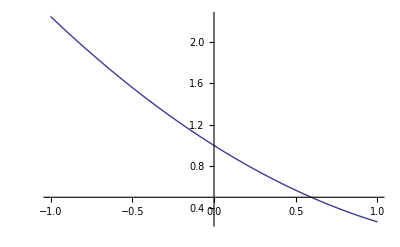

```mathematica
Plot[fun1D[x],{x,-1.,1.}]
```

```mathematica
NIntegrate[fun1D[x],{x,-1.,1.},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function (1.`  + x Sin[36] + x^2 Sin[72]) is less than WorkingPrecision (50.).

2.1692155751746908487126875090738376699063817829259

## Numeric Integration Rule Two Dimensional

```mathematica
Plot3D[fun2D[x,y],{x,-1.,1.},{y,-1,1}]
```

-Graphics3D-

```mathematica
NIntegrate[fun2D[x,y],{x,-1.,1.},{y,-1.,1.},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function (1.`  + y Sin[6] + y^2 Sin[12] + x Sin[36] + x^2 Sin[72]) is less than WorkingPrecision (50.).

3.6230005930154684018715427138244729500584455281477

```mathematica
NIntegrate[fun3D[x,y,z],{x,-1.,1.},{y,-1.,1.},{z,-1,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function (1.`  + z Sin[1] + z^2 Sin[2] + y Sin[6] + y^2 Sin[12] + x Sin[36] + x^2 Sin[72]) is less than WorkingPrecision (50.).

9.6707943242327546581324717367469321473229043134898